```mathematica
(* +----------------------------------- evaluate_pcf.nb -----------------------------+ *)
(* +                                                                                + *)
(* +           evaluate_pcf.nb calculates the pair correlation function for a        + *)
(* +           data set with xyz coordinates.                                        + *)
(* +                                                                                + *)
(* +                                                                                + *) 
(* +           INPUT:  xyz coodinates of the cluster                                + *)
(* +           OUTPUT: graph with the pair correlation function                     + *)         
(* +           USAGE:  (1) Delete All Output (from the 'Cell' menu)                  + *)
(* +                   (2) Fill the section between 'BEGIN USER INPUT' and           + *)
(* +                      'END USER INPUT'                                           + *)
(* +                   (3) Evaluate Notebook (from the'Evaluate' menu)              + *)
(* +           DEPENDENCIES: None                                                  + *)
(* +           NOTES:  Boundary effect are not take care of. The pair correlation   + *)
(* +                   function may therefore not converge to 1 for infinite         + *)
(* +                   distance. This is expected for finite size clusters and       + *)
(* +                   not a bug.                                                   + *) 
(* +                                                                                + *)
(* +           AUTHOR:  L. Houben, Weizmann Institute of Science                    + *)
(* +                    lothar.houben(at)weizmann.ac.il                             + *)
(* +           COPYRIGHT: This software is licensed under the GNU GENERAL PUBLIC    + *)
(* +                    LICENSE Version 3                                         + *)
(* +                                                                                + *)
(* +----------------------------------------------------------------------------------+ *)
(* +-------------------------- BEGIN USER INPUT --------------------------------------+ *)                                                                         
(* +-----------------------------------------------------------------------------------+ *)
(* baseDir is the base folder for program input and output.                            *)                        
(* dataDir is a subfolder that holds the data file.                                   *)
(* outDir is a subfolder for the program output files.                                  *)
(* Please make sure that the folders exist.                                           *)
baseDir=StringJoin[$HomeDirectory,"/Desktop/diOPA"];   
dataDir ="data";
outDir="out"
(* datafileName is name of the data file with the cluster xyz coordinates *)
datafileName="Ferritin-agglomerate.cel";
(* +----------------------------------------------------------------------------------+ *)
(* +-------------------------- END USER INPUT --------------------------------------+ *)                                                                         
(* +-----------------------------------------------------------------------------------+ *)
```

out

```mathematica
(*  define input files                                                   *)
celfile= StringJoin[baseDir,"/",dataDir,"/",datafileName]
```

/Users/lothar/Desktop/diOPA/data/Ferritin-agglomerate.cel

```mathematica
(*  define output files                                                   *)
graphfileprefix=StringJoin[baseDir,"/",outDir,"/",FileBaseName[datafileName],"_PCF"]
logfilename=StringJoin[baseDir,"/",outDir,"/",FileBaseName[datafileName],"_PCF.log"]
```

/Users/lothar/Desktop/diOPA/out/Ferritin-agglomerate_PCF

/Users/lothar/Desktop/diOPA/out/Ferritin-agglomerate_PCF.log

```mathematica
(* define plot parameters                                               *)
binwidth=0.1;
range={0,5};
```

```mathematica
(* +-----------------------------------------------------------------------------------------------------------------------------------------------+ *)
(*                                                                                                                                               *)
(* END PARAMETER DEFINITION                                                                                                                      *)
(*                                                                                                                                               *)
(* +-----------------------------------------------------------------------------------------------------------------------------------------------+ *)
```

```mathematica
(* +-----------------------------------------------------------------------------------------------------------------------------------------------+ *)
(*                                                                                                                                               *)
(* START FUNCTION DEFINITION                                                                                                                      *)
(*                                                                                                                                               *)
(* +-----------------------------------------------------------------------------------------------------------------------------------------------+ *)
```

```mathematica
(* ReadCelFile: Function for Reading a celfile *)
(* courtesy of J. Barthel, RWTH-Aachen University, Germany *)
(* Email: ju.barthel-at-fz-juelich.de *)
(* Reads super cell structure data in CEL file format from *)
(* The specified file and stores the information in global arrays: *)
(*   celdims = dimensions of the super-cell  *)
(*   celangs = angles between the super-cell axes  *)
(*   natoms  = number of atoms in the super-cell *)
(*  *)
ReadCelFile[filename_]:=Block[{celstrs},
(* - init *)
Clear[celdims,celangs,celatms,natoms];
celdims={0.,0.,0.};celangs={90.,90.,90.};celatms={};natoms=0;
(* - read data from file *)
celstrs=ReadList[filename,"String"];
(* - analyse / extract numeric data *)
celdims=Take[ReadList[StringToStream[celstrs[[2]]],"Number"],{2,4}];
celangs=Take[ReadList[StringToStream[celstrs[[2]]],"Number"],{5,7}];
celatms=Table[
ReadList[StringToStream[celstrs[[i]]],Join[{"Word"},Table["Number",{8}]]][[1]]
,{i,3,Length[celstrs]-1}];
natoms=Length[celatms];
(* - report *)
Print["- INPUT  CEL file: ",InputForm[filename]];
Print["- OUTPUT (celdims) dimensions  (a,b,c)  [nm]: ",celdims];
Print["- OUTPUT (celangs) axes angles (α,β,γ) [deg]: ",celangs];
Print["- OUTPUT (natoms)  number of atoms          : ",natoms];
If[natoms>0,
Print["- OUTPUT (celatms[[1]]) first atom          : ",celatms[[1]]];
];
If[natoms>1,
Print["- OUTPUT (celatms[[",natoms,"]]) last  atom          : ",celatms[[natoms]]];
];
]
```

```mathematica
(* BoundingBox: Returns box coordinates around the centre *)
(* in a list variable cutoff *)
(* INPUT: xyz_= {{x1,y1,z1},{x2, y2, z2}, ...}  *)
(*        margin = margin size to add               *)
(*                                 *)
(* OUTPUT: bbox ={{xmin-margin,xmax+margin},{ymin-mrgin,ymax+margin}{zmin-margin,zmax+margin}}  *)
BoundingBox[xyz_,margin_]:=Block[{tmp},
(* - init *)
Clear[bbox];
bbox={{0,0},{0,0},{0,0}};
bbox[[1,1]]=Min[xyz[[All,1]]]-margin;
bbox[[2,1]]=Min[xyz[[All,2]]]-margin;
bbox[[3,1]]=Min[xyz[[All,3]]]-margin;
bbox[[1,2]]=Max[xyz[[All,1]]]+margin;
bbox[[2,2]]=Max[xyz[[All,2]]]+margin;
bbox[[3,2]]=Max[xyz[[All,3]]]+margin;
bboxvol=(bbox[[1,2]]-bbox[[1,1]])*(bbox[[2,2]]-bbox[[2,1]])*(bbox[[3,2]]-bbox[[3,1]]);
axespos={bbox[[1,1]],bbox[[2,1]],bbox[[3,1]]};
Print["- BoundingBox         : ",bbox];
Print["- BoundingBox Volume  : ",bboxvol];
Print["- Axes Position       : ",axespos];
]
```

```mathematica
(* PCFMap *)
(* returns normalized pcf data in a list variable pcff *)
(* INPUT: xyz_= {{x1,y1,z1},{x2, y2, z2}, ...}  *)
(*        bwidth_= bin width                    *)
(* OUTPUT: pcf = list with pcf data             *)
PCFMap[xyz_,bwidth_,dens_]:=Block[{distlist={},v,kk,jj},
(* - init *)
Clear[pcf];
pcf={};
distlist={};
distlist=Outer[EuclideanDistance,xyz,Take[xyz,Floor[Length[xyz]/2]],1]//Flatten;
v=BinCounts[distlist,{bwidth,Max[distlist],bwidth}];
radius=Length[v]*bwidth;
Print["- Minimum distance       : ",Min[distlist]];
Print["- Maximum distance       : ",Max[distlist]];
Print["- Bin width              : ",bwidth];
Print["- NPairs                 : ",Length[distlist]];
For[jj=1, jj≤Length[v],{tmpr=(jj-1)*bwidth; tmpR=tmpr+bwidth; norm=(4*Pi*((tmpR*tmpR*tmpR)-(tmpr*tmpr*tmpr)));AppendTo[pcf,{(jj+0.5)*bwidth,v[[jj]]/norm/Length[xyz]/density}]}; jj++];
]
```

```mathematica
(* +-----------------------------------------------------------------------------------------------------------------------------------------------+ *)
(*                                                                                                                                               *)
(* END FUNCTION DEFINITION                                                                                                                      *)
(*                                                                                                                                               *)
(* +-----------------------------------------------------------------------------------------------------------------------------------------------+ *)
```

```mathematica
(* +-----------------------------------------------------------------------------------------------------------------------------------------------+ *)
(*                                                                                                                                               *)
(* START PROCESSING                                                                                                                      *)
(*                                                                                                                                               *)
(* +-----------------------------------------------------------------------------------------------------------------------------------------------+ *)
```

```mathematica
(* Open log file and start logging *)
logfile=OpenWrite[logfilename];
WriteString[logfile,"Filename:",celfile,"\n"];
```

```mathematica
(* Open data file and plot data *)
ReadCelFile[celfile];
Clear[coordatms,f,q];
(* Extract relative atomcoordinates only *)
coordatms=celatms[[All,{2,3,4}]];
(* multiply atom relative coordinates with cell dimensions *)
f[x_]:={celdims[[1]]*x[[1]],celdims[[2]]*x[[2]],celdims[[3]]*x[[3]]}
q=Map[f,coordatms];
(* Plot atoms *)
ListPointPlot3D[q,BoxRatios->{1,1,1},PlotStyle->PointSize[0.01],AxesLabel->{"x/Δ","y/Δ","z/Δ"},Lighting->"Neutral",LabelStyle->Directive[Bold]]
```

- INPUT  CEL file: "/Users/lothar/Desktop/diOPA/data/Ferritin-agglomerate.cel"

- OUTPUT (celdims) dimensions  (a,b,c)  [nm]: {19.6635,16.056,21.3574}

- OUTPUT (celangs) axes angles (α,β,γ) [deg]: {90.,90.,90.}

- OUTPUT (natoms)  number of atoms          : 559

- OUTPUT (celatms[[1]]) first atom          : {Fe,0.,0.514721,0.544393,1.,0.005,0.1,0.1,0.1}

- OUTPUT (celatms[[559]]) last  atom          : {Fe,1.,0.21619,0.073572,1.,0.005,0.1,0.1,0.1}

-Graphics3D-

```mathematica
WriteString[logfile,"- Number of atoms: ",ToString[Length[q]],"\n"];
```

```mathematica
BoundingBox[q,0]
density=Length[q]/bboxvol
```

- BoundingBox         : {{0.,19.6635},{0.493642,16.056},{0.,21.3429}}

- BoundingBox Volume  : 6531.16

- Axes Position       : {0.,0.493642,0.}

0.0855897

```mathematica
PCFMap[q,binwidth,density]
```

- Minimum distance       : 0.

- Maximum distance       : 25.0035

- Bin width              : 0.1

- NPairs                 : 155961

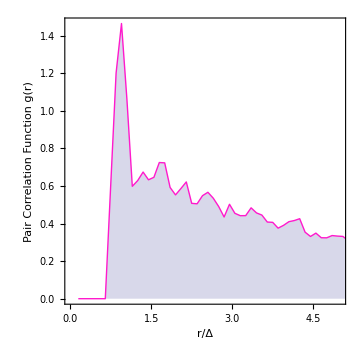

```mathematica
pcfplot=ListPlot[pcf,PlotRange->{{range[[1]],range[[2]]},All},PlotStyle->{Thick,RGBColor[1.,0.1,0.8]},Filling ->Axis,FillingStyle->Automatic, Joined->True,AxesLabel->{"r/Δ","Pair Correlation Function g(r)"},LabelStyle->Directive[Bold],AspectRatio->1,ImageSize->Medium,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Pair Correlation Function g(r)",None},{"r/Δ",None}},FrameTicks->All]
```

```mathematica
goutfile=StringJoin[graphfileprefix,".png"];
Export[goutfile,pcfplot,"AllowRasterization"->True,ImageResolution->600]
```

/Users/lothar/Desktop/diOPA/out/Ferritin-agglomerate_PCF.png

```mathematica
Close[logfile];
```

```mathematica
(* +-----------------------------------------------------------------------------------------------------------------------------------------------+ *)
(*                                                                                                                                               *)
(* END PROCESSING                                                                                                                      *)
(*                                                                                                                                               *)
(* +-----------------------------------------------------------------------------------------------------------------------------------------------+ *)
```